# Pulse Width Modulation (PWM)

## A prototype, self-teaching lesson with direct demonstrations

Egar Almeida

Flip Phillips & Daavid Väänänen

## Technical Explanation

## Frequency

We’ll begin the lesson by plotting a square wave

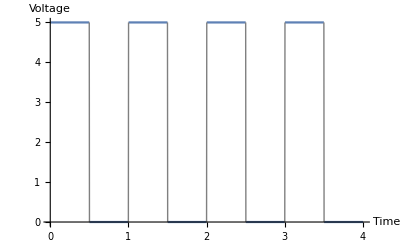

```mathematica
Plot[5 UnitStep[SquareWave[n]], {n,0,4},ExclusionsStyle-> Gray, AxesLabel->{"Time", "Voltage"}]
```

This square wave shows an alternation between 0 and 5 volts: We see 5 volts for a duration of half a second, then 0 volts for a duration of half a second.

This wave can be read as “a square wave of 1Hz with a 50% duty cycle”.

Hz (Hertz) is the frequency of the wave. 1Hz means 1 cycle per second.

Duty cycle is the portion of time during each cycle where the wave is at 5 volts, also known as “On” time (or HIGH in Arduino). 50% means that we have 5 volts for half the time and 0 volts for half the time.

If we were to connect an LED to a microcontroller pin outputting this wave, we’d get a blinking LED. In Arduino, we could do it with:

void loop() {
	digitalWrite(LED_PIN, HIGH);	// Turn LED on
	delay(500);					// Wait for 500 mS (half a second)
	digitalWrite(LED_PIN, LOW);		// Turn LED off
	delay(500);					// Wait for 500 mS again
}

This will produce the following result:

What happens when we increase the frequency of this wave?
The LED would blink faster, but frequencies above 60hz would make it impossible for the human eye to distinguish the flickering due to flicker fusion and it’d seem like the LED is fully ON all the time.

Try varying the frequency of the square wave to see the waveform representation:

## Duty Cycle

Now that we’ve seen what altering the frequency does, let’s examine what happens when we alter the duty cycle between 10% and 100% at a constant frequency.

## Demonstrations

## Setup

In order to demonstrate the concepts explained above, we are going to use Arduino. Connect an LED to pin 9 in series with a 220 Ohm resistor:

-Graphics-

Next, let’s do some setup. Enter the port where your Arduino is connected, here: